# CaffeLink

## ImageNet example

## Requirements and Initialization

This example shows how to use CaffeLink to test AlexNet and visualize its features. It relies on examples from Caffe, which can be found here. Trained model can be obtained from Caffe Model Zoo. This document is only concerned with CaffeLink, so for details regarding net design please refer to Caffe.

Caffe is a command line tool and it would be inefficient to somehow transmit all its output to Mathematica. So it is highly recommended to launch Mathematica session with terminal. CaffeLink also relies on stoud.

### Initialize CaffeLink

The first think to do is load CaffeLink module and initialize it with path to caffe.proto protobuffer definition of all parameters Caffe uses.

```mathematica
caffeDir = "...";
```

```mathematica
Needs["CaffeLink`",FileNameJoin[{NotebookDirectory[],"../caffeLink.m"}]];
initCaffeLinkModule[FileNameJoin[{caffeDir,"src/caffe/proto/caffe.proto"}]];
```

Before training, testing etc. CaffeLink library must be initialized. That is: choose data type (double or float), computing mode (GPU or CPU) and device ID for GPU mode.

```mathematica
initCaffeLink["UseDouble"->True,"UseGPU"->True,"GPUDevice"->0]
```

True

Mode can be switched later, data type not.

## Net

### Testing

Net testing requires a net and net parameters, referred by Caffe as deploy proto. The main difference between deploy and training proto is in input definition, the rest can be the same.

#### Deploy

```mathematica
netDeployParam = ReadString[FileNameJoin[
	{caffeDir,"models/bvlc_reference_caffenet/deploy.prototxt"}]
	];
```

#### Test

Tested net must be prepared at first. Caffe allocates memory and creates net topology based on given deploy proto. Preparation is done either from string with prepareNetString or from file path using prepareNetFile.

```mathematica
prepareNetString[netDeployParam]
```

Net info can be printed (to console) with printNetInfo.

```mathematica
printNetInfo[]
```

After preparation, any net data with the same topology can be loaded.

```mathematica
loadNet[FileNameJoin[
	{caffeDir,"models/bvlc_reference_caffenet/bvlc_reference_caffenet.caffemodel"}]
	]
```

That also allows extracting learned parameters (weights, filters, etc.).

Caffe provide one testing image, so lets use it.

```mathematica
testImg = Import[FileNameJoin[{caffeDir,"examples/images/cat.jpg"}]];
```

Deploy defines 10 input images with size 227x227.

```mathematica
h = 227; w = 227;
If[ImageDimensions[testImg][[1]]>ImageDimensions[testImg][[2]],
	testImg = ImageRotate[testImg];
	testImg = ImageResize[testImg,w];
	testImg = ImageRotate[testImg,-90 Degree];
	,
	testImg=ImageResize[testImg,w];
];

inputImgs={};
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Right,Top}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Left,Top}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Right,Bottom}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Left,Bottom}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h}]];
testImg=ImageReflect[testImg,Left->Right];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Right,Top}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Left,Top}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Right,Bottom}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h},{Left,Bottom}]];
AppendTo[inputImgs,ImageCrop[testImg,{w,h}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Caffe requires channels separated.

```mathematica
input={};
For[i=1,i<=10,i++,
chs=ColorSeparate[inputImgs[[i]]];
AppendTo[input,ImageData[chs[[3]]]];
AppendTo[input,ImageData[chs[[2]]]];
AppendTo[input,ImageData[chs[[1]]]];
];
{Image[input[[28]]],Image[input[[29]]],Image[input[[30]]]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
setInput[Flatten[input]*255]
```

This runs the test.

```mathematica
evaluateNet[]
```

Result can be obtained from top blob of the last layer.

```mathematica
result = getTopBlob["prob"];
```

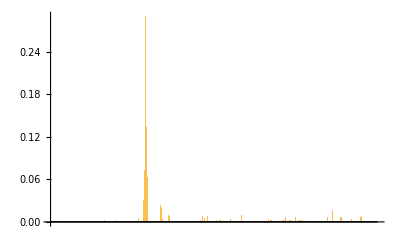

```mathematica
res = ArrayReshape[result,{10,1000}];
BarChart[res[[1]]] (* probabilities of the first image *)
```

In order to visualize image classification we have to import class names:

```mathematica
classes = Module[{raw,noId},
	raw = Import[FileNameJoin[{caffeDir, "data/ilsvrc12/synset_words.txt"}], {"Text", "Lines"}];
	noId = StringSplit[#][[2 ;;]] & /@ raw;
	StringTrim[StringJoin[#[[;;Min[Length[#],2]]]],","]& /@ noId
];
```

This shows five most probable classes for image 1 and 10.

```mathematica
classifyBestFive[probs_]:=
Module[{pairs, best},
	pairs = Transpose[{probs, classes}];
	best = Transpose[Reverse[Reverse[SortBy[pairs, First]][[;;5]]]];
	BarChart[best[[1]]*100.0,
		BarOrigin->Left,
		ChartLabels->Placed[best[[2]],After],
		Frame->{True,False,False,False},
		PlotRange -> {{0, 100},Automatic},
		PlotRangePadding->{{0,65},0},
		FrameLabel->"probability %",
		BaseStyle->{FontSize->10},
		ImageSize->130
	]
]

selected = {1,10};
Grid[Partition[MapThread[Grid[{{ImageResize[#1,130],classifyBestFive[#2]}}]&, 
	{inputImgs[[selected]],res[[selected]]}],2],Frame->All]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

### Extracting features

Functions getParamBlob, getTopBlob and getBottomBlob allow inspection of all blobs in net. In combination with setParamBlob weights can be easily copied to another layer or to completely different net.

#### Visualization

In short: get parameters, separate and reshape them and then render.

Layer conv1 - filters

```mathematica
par = getParamBlob["conv1"]; (* 0th layer: conv1, 0th par. blob - filters *)
```

```mathematica
fn = 96;
filters = ArrayReshape[par,{96,3,11,11}]; (* conv1 has 96 filters, 11x11 *)
filters = Map[Rescale,filters];
fImgs = {};
f = Map[Image[#]&,filters,{2}];
For[i = 1,i ≤ fn,i++,
	AppendTo[fImgs,ColorCombine[{f[[i,3]],f[[i,2]],f[[i,1]]},"RGB"]];
];
fImgs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Layer conv1 - features

```mathematica
in = getBottomBlob["conv1"];
out = getTopBlob["conv1"];
```

This shows one input image and result after convolution (20 filters).

```mathematica
Map[Image[#,Magnification->2]&,outImgs[[imgi,1;;fn]],1]
```

```mathematica
Image[outImgs[[imgi,1]]]
```

```mathematica
imgi = 1; (* test image index, 1 - 10 *)
inImg = ArrayReshape[in,{10,3,h,w}]/255;
f = Map[Image[#]&,inImg,{2}];
inImg = ColorCombine[{f[[imgi,3]],f[[imgi,2]],f[[imgi,1]]},"RGB"];

outImgs = ArrayReshape[out/255,{10,96,55,55}][[imgi]];
{Image[inImg,Magnification->1],
Map[Image[#,Magnification->1]&,outImgs[[1;;fn]],1]}
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The same in range 0, 1 :

```mathematica
outImgs = Map[Rescale,outImgs];
Map[Image[#,Magnification->1]&,outImgs[[1;;fn]],1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}